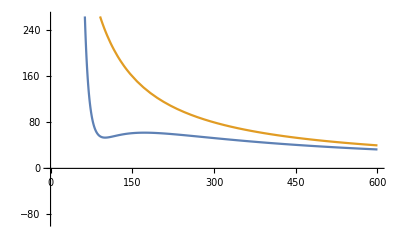

```mathematica
T:=288.7
a:=3.658*10^6
b:=42.75
R:=83.14462618
preal[V_]:=(R T)/(V-b)-a/V^2
pideal[V_]:=(R T)/V
Plot[{preal[V], pideal[V]},{V,0,600}]
```